# Omicron analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-countries

```mathematica
dataset="omicron-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={};
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-11-01

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-02-27

```mathematica
countries=Union[seqData[[All,2]]]
```

{Australia,Austria,Brazil,Canada,Croatia,Denmark,France,Germany,India,Israel,Japan,Netherlands,New Zealand,Norway,Romania,Singapore,Slovakia,South Africa,South Korea,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

```mathematica
countries=Complement[countries,countriesToDrop]
```

{Australia,Austria,Brazil,Canada,Croatia,Denmark,France,Germany,India,Israel,Japan,Netherlands,New Zealand,Norway,Romania,Singapore,Slovakia,South Africa,South Korea,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countryVariantCounts[country_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==country&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
countrySequenceCounts[country_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==country][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->countrySequenceCounts[#][[-15;;-1]]&,countries]
```

{Australia→{{2022-02-13,145},{2022-02-14,141},{2022-02-15,77},{2022-02-16,71},{2022-02-17,119},{2022-02-18,36},{2022-02-19,43},{2022-02-20,53},{2022-02-21,112},{2022-02-22,84},{2022-02-23,61},{2022-02-24,65},{2022-02-25,32},{2022-02-26,8},{2022-02-27,0}},Austria→{{2022-02-13,43},{2022-02-14,10},{2022-02-15,106},{2022-02-16,174},{2022-02-17,71},{2022-02-18,0},{2022-02-19,0},{2022-02-20,0},{2022-02-21,5},{2022-02-22,75},{2022-02-23,263},{2022-02-24,6},{2022-02-25,0},{2022-02-26,0},{2022-02-27,0}},Brazil→{{2022-02-13,3},{2022-02-14,32},{2022-02-15,12},{2022-02-16,0},{2022-02-17,1},{2022-02-18,0},{2022-02-19,0},{2022-02-20,0},{2022-02-21,0},{2022-02-22,0},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0},{2022-02-26,0},{2022-02-27,0}},Canada→{{2022-02-13,117},{2022-02-14,121},{2022-02-15,187},{2022-02-16,123},{2022-02-17,84},{2022-02-18,80},{2022-02-19,68},{2022-02-20,43},{2022-02-21,28},{2022-02-22,38},{2022-02-23,63},{2022-02-24,0},{2022-02-25,0},{2022-02-26,0},{2022-02-27,0}},Croatia→{{2022-02-13,0},{2022-02-14,50},{2022-02-15,122},{2022-02-16,59},{2022-02-17,73},{2022-02-18,74},{2022-02-19,0},{2022-02-20,0},{2022-02-21,0},{2022-02-22,0},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0},{2022-02-26,0},{2022-02-27,0}},Denmark→{{2022-02-13,2382},{2022-02-14,2376},{2022-02-15,2658},{2022-02-16,1365},{2022-02-17,1662},{2022-02-18,2625},{2022-02-19,1430},{2022-02-20,1104},{2022-02-21,1609},{2022-02-22,1417},{2022-02-23,671},{2022-02-24,1581},{2022-02-25,1422},{2022-02-26,1499},{2022-02-27,621}},France→{{2022-02-13,182},{2022-02-14,1768},{2022-02-15,97},{2022-02-16,80},{2022-02-17,38},{2022-02-18,98},{2022-02-19,34},{2022-02-20,42},{2022-02-21,1313},{2022-02-22,59},{2022-02-23,45},{2022-02-24,20},{2022-02-25,24},{2022-02-26,0},{2022-02-27,0}},Germany→{{2022-02-13,213},{2022-02-14,1310},{2022-02-15,1188},{2022-02-16,376},{2022-02-17,287},{2022-02-18,126},{2022-02-19,6},{2022-02-20,8},{2022-02-21,14},{2022-02-22,1},{2022-02-23,1},{2022-02-24,0},{2022-02-25,0},{2022-02-26,0},{2022-02-27,0}},India→{{2022-02-13,95},{2022-02-14,258},{2022-02-15,233},{2022-02-16,272},{2022-02-17,148},{2022-02-18,196},{2022-02-19,99},{2022-02-20,36},{2022-02-21,133},{2022-02-22,54},{2022-02-23,66},{2022-02-24,112},{2022-02-25,5},{2022-02-26,0},{2022-02-27,0}},Israel→{{2022-02-13,0},{2022-02-14,0},{2022-02-15,0},{2022-02-16,0},{2022-02-17,0},{2022-02-18,0},{2022-02-19,0},{2022-02-20,0},{2022-02-21,0},{2022-02-22,0},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0},{2022-02-26,0},{2022-02-27,0}},Japan→{{2022-02-13,9},{2022-02-14,45},{2022-02-15,17},{2022-02-16,19},{2022-02-17,7},{2022-02-18,4},{2022-02-19,11},{2022-02-20,4},{2022-02-21,5},{2022-02-22,2},{2022-02-23,0},{2022-02-24,0},{2022-02-25,1},{2022-02-26,0},{2022-02-27,0}},Netherlands→{{2022-02-13,125},{2022-02-14,212},{2022-02-15,182},{2022-02-16,195},{2022-02-17,99},{2022-02-18,102},{2022-02-19,72},{2022-02-20,59},{2022-02-21,60},{2022-02-22,28},{2022-02-23,14},{2022-02-24,1},{2022-02-25,4},{2022-02-26,0},{2022-02-27,0}},New Zealand→{{2022-02-13,70},{2022-02-14,90},{2022-02-15,79},{2022-02-16,64},{2022-02-17,39},{2022-02-18,63},{2022-02-19,22},{2022-02-20,68},{2022-02-21,43},{2022-02-22,37},{2022-02-23,20},{2022-02-24,0},{2022-02-25,0},{2022-02-26,0},{2022-02-27,0}},Norway→{{2022-02-13,83},{2022-02-14,47},{2022-02-15,38},{2022-02-16,40},{2022-02-17,48},{2022-02-18,10},{2022-02-19,10},{2022-02-20,43},{2022-02-21,15},{2022-02-22,11},{2022-02-23,11},{2022-02-24,19},{2022-02-25,1},{2022-02-26,0},{2022-02-27,0}},Romania→{{2022-02-13,5},{2022-02-14,7},{2022-02-15,70},{2022-02-16,7},{2022-02-17,2},{2022-02-18,7},{2022-02-19,5},{2022-02-20,2},{2022-02-21,1},{2022-02-22,0},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0},{2022-02-26,0},{2022-02-27,0}},Singapore→{{2022-02-13,26},{2022-02-14,59},{2022-02-15,12},{2022-02-16,32},{2022-02-17,50},{2022-02-18,25},{2022-02-19,29},{2022-02-20,22},{2022-02-21,57},{2022-02-22,58},{2022-02-23,5},{2022-02-24,48},{2022-02-25,10},{2022-02-26,0},{2022-02-27,0}},Slovakia→{{2022-02-13,4},{2022-02-14,24},{2022-02-15,16},{2022-02-16,132},{2022-02-17,34},{2022-02-18,14},{2022-02-19,1},{2022-02-20,3},{2022-02-21,1},{2022-02-22,0},{2022-02-23,93},{2022-02-24,0},{2022-02-25,0},{2022-02-26,0},{2022-02-27,0}},South Africa→{{2022-02-13,0},{2022-02-14,10},{2022-02-15,6},{2022-02-16,10},{2022-02-17,13},{2022-02-18,8},{2022-02-19,0},{2022-02-20,0},{2022-02-21,2},{2022-02-22,1},{2022-02-23,2},{2022-02-24,0},{2022-02-25,0},{2022-02-26,0},{2022-02-27,0}},South Korea→{{2022-02-13,0},{2022-02-14,0},{2022-02-15,0},{2022-02-16,0},{2022-02-17,0},{2022-02-18,0},{2022-02-19,0},{2022-02-20,0},{2022-02-21,0},{2022-02-22,0},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0},{2022-02-26,0},{2022-02-27,0}},Spain→{{2022-02-13,44},{2022-02-14,179},{2022-02-15,209},{2022-02-16,151},{2022-02-17,124},{2022-02-18,102},{2022-02-19,26},{2022-02-20,12},{2022-02-21,53},{2022-02-22,21},{2022-02-23,23},{2022-02-24,13},{2022-02-25,15},{2022-02-26,0},{2022-02-27,0}},Sweden→{{2022-02-13,99},{2022-02-14,893},{2022-02-15,392},{2022-02-16,265},{2022-02-17,253},{2022-02-18,97},{2022-02-19,100},{2022-02-20,33},{2022-02-21,106},{2022-02-22,28},{2022-02-23,38},{2022-02-24,31},{2022-02-25,1},{2022-02-26,0},{2022-02-27,0}},Switzerland→{{2022-02-13,442},{2022-02-14,624},{2022-02-15,313},{2022-02-16,384},{2022-02-17,187},{2022-02-18,132},{2022-02-19,225},{2022-02-20,192},{2022-02-21,525},{2022-02-22,217},{2022-02-23,160},{2022-02-24,52},{2022-02-25,3},{2022-02-26,0},{2022-02-27,0}},Thailand→{{2022-02-13,4},{2022-02-14,5},{2022-02-15,0},{2022-02-16,0},{2022-02-17,0},{2022-02-18,0},{2022-02-19,0},{2022-02-20,0},{2022-02-21,0},{2022-02-22,0},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0},{2022-02-26,0},{2022-02-27,0}},United Kingdom→{{2022-02-13,8308},{2022-02-14,12268},{2022-02-15,10476},{2022-02-16,8729},{2022-02-17,8930},{2022-02-18,7483},{2022-02-19,7469},{2022-02-20,6447},{2022-02-21,10494},{2022-02-22,8341},{2022-02-23,8003},{2022-02-24,4106},{2022-02-25,4335},{2022-02-26,2555},{2022-02-27,1614}},USA→{{2022-02-13,3416},{2022-02-14,6112},{2022-02-15,5608},{2022-02-16,5864},{2022-02-17,4089},{2022-02-18,3491},{2022-02-19,2022},{2022-02-20,1354},{2022-02-21,1879},{2022-02-22,1384},{2022-02-23,354},{2022-02-24,414},{2022-02-25,99},{2022-02-26,0},{2022-02-27,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[country_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==country,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.00001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{logitTransform[0.0005],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[country_]:=Map[logisticPrevSeries[countryVariantCounts[country,#],countrySequenceCounts[country]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForCountries=Map[freqForCountry,countries];
```

```mathematica
modeledFreqsForCountries=Map[{modeledLogisticPrevSeries[logisticPrevSeries[countryVariantCounts[#,"Omicron"],countrySequenceCounts[#]]]}&,countries];
```

```mathematica
legendsForCountries=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForCountries];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-countries_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-countries_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[country_,variant_]:=Module[{countryVariantFrequencyDateSeries,countryCasesDateSeries,tuples},
countryVariantFrequencyDateSeries=smoothedPrevalence[countryVariantCounts[country,variant],countrySequenceCounts[country]];
countryCasesDateSeries=csGather[country];
tuples=compareWithDate[countryVariantFrequencyDateSeries,countryCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
panels=Map[splitCasePlot,countries];
```

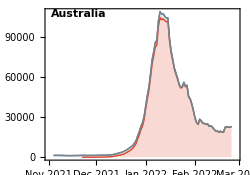
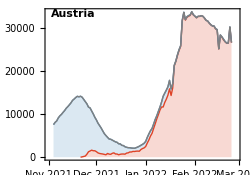
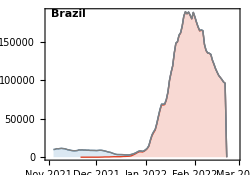
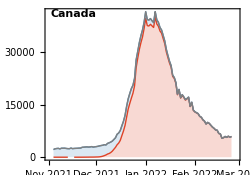
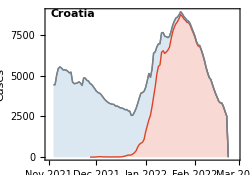
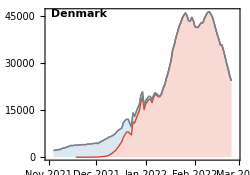
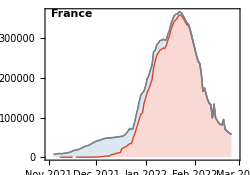
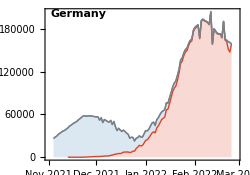
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=500000;
```

```mathematica
splitCaseLogPlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[country_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000,1000000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[country_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[country,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->200,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{50,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000,1000000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.88,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForCountries=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,countries];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{countries,legendsForCountries}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_partitioned-log-cases.png